## 1. Элементарная описательная статистика

```mathematica
data = RandomReal[30, 15]
```

{23.3651,4.11753,6.40254,2.54647,10.1229,13.2355,18.406,5.40074,15.7298,9.60588,21.885,5.60396,27.5783,7.27426,10.296}

```mathematica
Mean[data]                                                                              (*Среднее арифметическое*)
```

12.1047

```mathematica
Median[data]                                                                              (*Серединное значение или среднее арифметическое 2 серединных значений*)
```

10.1229

```mathematica
Max[data]                                                                              (*Максимальное значение*)
```

27.5783

```mathematica
Variance[data]                                                                              (*Дисперсия–это средний квадрат отклонений.То есть вначале рассчитывается среднее значение,затем берется разница между каждым исходным и средним значением,возводится в квадрат,складывается и затем делится на количество значений в данной совокупности*)
```

59.1183

```mathematica
StandardDeviation[data]                                                                              (*Среднеквадратичное отклонение (корень дисперсии)*)
```

7.68884

```mathematica
Quantile[data,0.5]                                                                              (*Значение, которое заданная случайная величина не превышает с фиксированной вероятностью*)
```

10.1229

```mathematica
Quartiles[data]                                                                                       (*Квантили 0.25 (нижний квантиль), 0.5 (медиана), 0.75 (верхний квантиль)*)
```

{5.8036,10.1229,17.7369}

## 2. Работа со статистическими распределениями

```mathematica
PDF[NormalDistribution[2,5],x^2]                            (*NormalDistribution - представляет собой нормальное (гауссово) распределение со средним значением μ и стандартным отклонением σ*)                     
(*PDF - Плотность распределения вероятностей непрерывной случайной величины Х есть функция f(x)–первая производная от функции распределения F(x)*)
```

(ⅇ^(-1/50 (-2+x^2)^2))/(5 √(2 π))

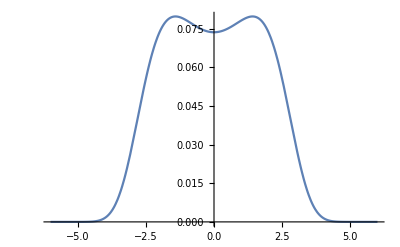

```mathematica
Plot[PDF[NormalDistribution[2,5],x^2],{x,-6,6}]
```

```mathematica
Mean[BinomialDistribution[50,0.4]]                                               (*BinomialDistribution - представляет биномиальное распределение с n испытаниями и вероятностью успеха p*)
```

20.

```mathematica
CharacteristicFunction[CauchyDistribution[2,5],x]                                  
(*CauchyDistribution - представляет распределение Коши с параметром местоположения a и параметром масштаба b*)
(*CharacteristicalFunction - дает характеристическую функцию распределения dist как функцию переменной t*)
```

ⅇ^(2 ⅈ x-5 x Sign[x])

```mathematica
Moment[PoissonDistribution[5],x]                                                               
(*Moment - числовая характеристика распределения данной случайной величины*)
(*PoissonDistribution - представляет распределение Пуассона со средним значением μ*)
```

Piecewise[{{BellB[x,5], x≥0}, {0, True}}]

```mathematica
RandomVariate[ChiSquareDistribution[10],5]                                                  
(*RandomVariate - дает псевдослучайную переменную из символического распределения*)
(*ChiSquareDistribution - представляет распределение χ^2 со степенями свободы ν*)
```

{15.3533,9.01186,6.89204,7.80928,7.82331}

```mathematica
data2=RandomVariate[GammaDistribution[5,10],10^4];                                                    
(*GammaDistribution - представляет собой гамма-распределение с параметром формы α и параметром масштаба β.*)
```

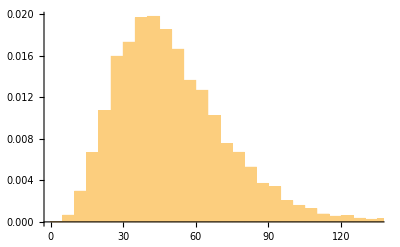

```mathematica
hist=Histogram[data2,Automatic,"ProbabilityDensity"]
```

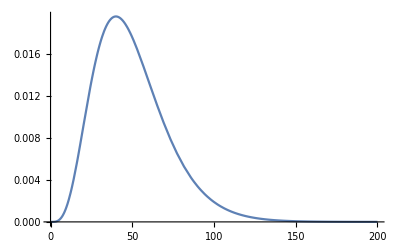

```mathematica
pl=Plot[PDF[GammaDistribution[5,10],x],{x,0,200}]
```

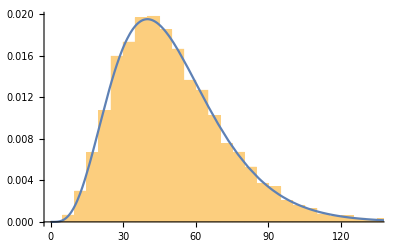

```mathematica
Show[hist,pl]
```

```mathematica
alphabeta=FindDistributionParameters[data2,GammaDistribution[α,β]]
```

{α→5.0141,β→9.98964}

```mathematica
gdist=EstimatedDistribution[data2,GammaDistribution[α,β]]
```

GammaDistribution[5.0141,9.98964]

```mathematica
LogLikelihood[gdist,gdata]                                               (*это совместное распределение выборки из параметрического распределения,рассматриваемое как функция параметра*)
```

LogLikelihood[GammaDistribution[5.0141,9.98964],gdata]

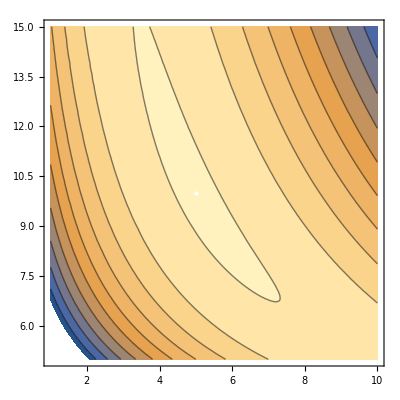

```mathematica
ContourPlot[LogLikelihood[GammaDistribution[α,β],data2],{α,1,10},{β,5,15},Epilog->{White,Point[{α,β}/. alphabeta]}]
```

## 3. Проверка гипотез о математическом ожидании

```mathematica
data=RandomVariate[NormalDistribution[5,2],15]
```

{6.03917,5.32821,5.35379,5.31145,8.3775,6.18243,5.41532,6.81673,6.7222,1.72133,3.99275,4.45166,6.47178,3.53686,2.26454}

```mathematica
TTest[data,5]                           (*Это вернет p-значение теста с нулевой гипотезой о том, что среднее значение генеральной совокупности равно 5*)
```

0.669999

```mathematica
TTest[data,5,AlternativeHypothesis->"Less"]                  (*одностороннее значение теста при альтернативной гипотезе о том,что среднее значение меньше 5*)
```

0.665001

```mathematica
data2=RandomVariate[NormalDistribution[4,1],15];
TTest[{data,data2}]                                                   (*используем TTest,чтобы определить,значительно ли разница между двумя средними значениями совокупности отличается от предполагаемого значения*)
```

0.0632307

```mathematica
TTest[{data,data2},5,AlternativeHypothesis->"Less"]                 (*Протестируем с нулевой гипотезой,              что среднее значение популяции данных на 5 больше чем у data2*)
```

8.67106×10^-9

```mathematica
PairedTTest[{data,data2}]                            (*проведем тесты для парных сравнений наборов данных*)
```

0.110576

## 4. Работа со столбцами данных

```mathematica
data=BlockRandom[SeedRandom[2];
RandomInteger[10,{7,5}]]
```

{{8,4,5,4,7},{4,0,1,0,4},{3,7,3,0,2},{7,8,7,9,3},{6,2,3,8,9},{1,3,8,5,5},{2,3,9,5,4}}

```mathematica
MatrixForm[data]
```

(8 | 4 | 5 | 4 | 7
4 | 0 | 1 | 0 | 4
3 | 7 | 3 | 0 | 2
7 | 8 | 7 | 9 | 3
6 | 2 | 3 | 8 | 9
1 | 3 | 8 | 5 | 5
2 | 3 | 9 | 5 | 4)

```mathematica
Grid[data]
```

8 | 4 | 5 | 4 | 7
4 | 0 | 1 | 0 | 4
3 | 7 | 3 | 0 | 2
7 | 8 | 7 | 9 | 3
6 | 2 | 3 | 8 | 9
1 | 3 | 8 | 5 | 5
2 | 3 | 9 | 5 | 4

```mathematica
Mean[data]                                  (*Среднее значение каждого столбца*)
```

{31/7,27/7,36/7,31/7,34/7}

```mathematica
StandardDeviation[data]                                  (*Среднеквадратичное отклонение каждого столбца*)
```

{√(146/21),2 √(41/21),√(185/21),√(86/7),√(122/21)}

```mathematica
Median[data]                                   (*Медиана каждого столбца*)
```

{4,3,5,5,4}

```mathematica
data[[All,1]]                                     (*Выбираем первый столбец*)
```

{8,4,3,7,6,1,2}

```mathematica
Mean[data[[All,1]]]                  (*Среднее значение первого столбца*)
```

31/7

```mathematica
StandardDeviation[data[[All,1]]]                      (*Среднеквадратичное отклонение первого столбца*)
```

√(146/21)

```mathematica
Median[data[[All,1]]]                                            (*Медиана первого столбца*)
```

4

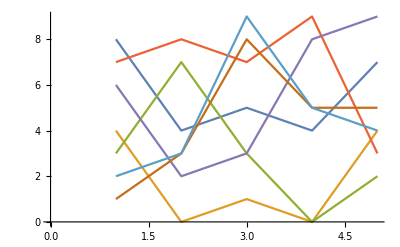

```mathematica
ListLinePlot[data]
```

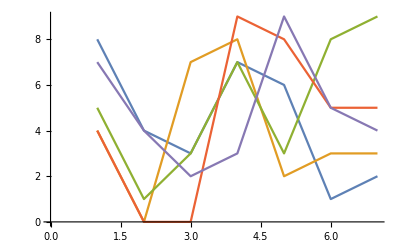

```mathematica
ListLinePlot[Transpose[data]]
```

```mathematica
Map[Normalize,Transpose[data]]                   (*Применяем функцию нормализации для каждой строки*)
```

{{8/(√179),4/(√179),3/(√179),7/(√179),6/(√179),1/(√179),2/(√179)},{4/(√151),0,7/(√151),8/(√151),2/(√151),3/(√151),3/(√151)},{5/(√238),1/(√238),3/(√238),√(7/34),3/(√238),4 √(2/119),9/(√238)},{4/(√211),0,0,9/(√211),8/(√211),5/(√211),5/(√211)},{7/(10 √2),(√2)/5,1/(5 √2),3/(10 √2),9/(10 √2),1/(2 √2),(√2)/5}}

```mathematica
Transpose[%]
```

{{8/(√179),4/(√151),5/(√238),4/(√211),7/(10 √2)},{4/(√179),0,1/(√238),0,(√2)/5},{3/(√179),7/(√151),3/(√238),0,1/(5 √2)},{7/(√179),8/(√151),√(7/34),9/(√211),3/(10 √2)},{6/(√179),2/(√151),3/(√238),8/(√211),9/(10 √2)},{1/(√179),3/(√151),4 √(2/119),5/(√211),1/(2 √2)},{2/(√179),3/(√151),9/(√238),5/(√211),(√2)/5}}

```mathematica
Map[Max, Transpose[data]]
```

{8,8,9,9,9}

## 5. Выполнение операций с подгруппами данных

```mathematica
agdata = {{clay, seedB, 175}, {silty, seedB, 180}, {clay, seedB,165}, {peaty, seedB, 183}, {peaty, seedB, 180}, {sandy, seedA, 168}, {clay, seedA, 184}, {sandy, seedB,171}, {sandy, seedB, 173}, {sandy, seedA, 189}, {clay, seedA, 192}, {peaty, seedB, 174}, {clay, seedA, 184}, {sandy, seedA, 182}, {sandy, seedB,177}, {silty, seedA, 180}, {clay, seedB, 175}, {silty, seedB, 181}, {peaty, seedA, 190}, {peaty, seedA,  192}, {silty, seedB, 190}, {peaty, seedA, 190}};
```

```mathematica
bySoilType=GatherBy[agdata,First]              (*Данные можно сгруппировать по типу почвы,используя First с GatherBy*)
```

{{{clay,seedB,175},{clay,seedB,165},{clay,seedA,184},{clay,seedA,192},{clay,seedA,184},{clay,seedB,175}},{{silty,seedB,180},{silty,seedA,180},{silty,seedB,181},{silty,seedB,190}},{{peaty,seedB,183},{peaty,seedB,180},{peaty,seedB,174},{peaty,seedA,190},{peaty,seedA,192},{peaty,seedA,190}},{{sandy,seedA,168},{sandy,seedB,171},{sandy,seedB,173},{sandy,seedA,189},{sandy,seedA,182},{sandy,seedB,177}}}

```mathematica
Table[{x[[1,1]],N[Mean[x[[All,-1]]]]},{x,bySoilType}]                             (*Среднюю урожайность по типу почвы можно рассчитать,извлекая тип почвы из каждого списка и вычисляя среднее значение урожайности (последние элементы) в списке*)
```

{{clay,179.167},{silty,182.75},{peaty,184.833},{sandy,176.667}}

```mathematica
bySeedType=GatherBy[agdata,#[[2]]&]                  (*Чтобы получить информацию об урожайности на основе типа семян,сначала сгруппируем данные по второму элементу каждой точки данных*)
```

{{{clay,seedB,175},{silty,seedB,180},{clay,seedB,165},{peaty,seedB,183},{peaty,seedB,180},{sandy,seedB,171},{sandy,seedB,173},{peaty,seedB,174},{sandy,seedB,177},{clay,seedB,175},{silty,seedB,181},{silty,seedB,190}},{{sandy,seedA,168},{clay,seedA,184},{sandy,seedA,189},{clay,seedA,192},{clay,seedA,184},{sandy,seedA,182},{silty,seedA,180},{peaty,seedA,190},{peaty,seedA,192},{peaty,seedA,190}}}

```mathematica
Table[{x[[1,2]],N[Mean[x[[All,-1]]]]},{x,bySeedType}]
```

{{seedB,177.},{seedA,185.1}}

```mathematica
Table[{x[[1,2]],{N[Min[x[[All,-1]]]],N[Max[x[[All,-1]]]]}},{x,bySeedType}]
```

{{seedB,{165.,190.}},{seedA,{168.,192.}}}

```mathematica
meddata={{drugB,67,18},{drugB,48,18},{drugA,33,16},{drugB,33,3},{placebo,40,15},{drugB,78,28},{drugB,54,13},{placebo,46,23},{drugA,36,12},{drugA,78,40},{placebo,77,37},{drugC,30,18},{drugC,45,23},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24},{drugB,75,25},{drugB,22,3},{placebo,51,25},{drugC,21,17},{placebo,27,8},{placebo,47,20},{placebo,69,34},{drugB,52,16},{drugC,73,34},{drugC,65,26}};
```

```mathematica
byDrug=GatherBy[meddata,First]
```

{{{drugB,67,18},{drugB,48,18},{drugB,33,3},{drugB,78,28},{drugB,54,13},{drugB,75,25},{drugB,22,3},{drugB,52,16}},{{drugA,33,16},{drugA,36,12},{drugA,78,40},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24}},{{placebo,40,15},{placebo,46,23},{placebo,77,37},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}},{{drugC,30,18},{drugC,45,23},{drugC,21,17},{drugC,73,34},{drugC,65,26}}}

```mathematica
describe[values_]:={Length[values],Mean[values],Median[values],{Min[values],Max[values]}}
```

```mathematica
Table[{x[[1,1]],describe[N[x[[All,-1]]]]},{x,byDrug}]
```

{{drugB,{8,15.5,17.,{3.,28.}}},{drugA,{7,23.1429,18.,{12.,40.}}},{placebo,{7,23.1429,23.,{8.,37.}}},{drugC,{5,23.6,23.,{17.,34.}}}}

```mathematica
byAgeGroup=GatherBy[meddata,IntegerPart[#[[2]]/10]&]                       (*Группировка по первой цифре второго значения списков*)
```

{{{drugB,67,18},{placebo,69,34},{drugC,65,26}},{{drugB,48,18},{placebo,40,15},{placebo,46,23},{drugC,45,23},{drugA,45,16},{placebo,47,20}},{{drugA,33,16},{drugB,33,3},{drugA,36,12},{drugC,30,18},{drugA,36,18}},{{drugB,78,28},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugB,75,25},{drugC,73,34}},{{drugB,54,13},{drugA,58,24},{placebo,51,25},{drugB,52,16}},{{drugB,22,3},{drugC,21,17},{placebo,27,8}}}

```mathematica
Table[{10 IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byAgeGroup}]//Sort
```

{{20,{3,9.33333,8.,{3.,17.}}},{30,{5,13.4,16.,{3.,18.}}},{40,{6,19.1667,19.,{15.,23.}}},{50,{4,19.5,20.,{13.,25.}}},{60,{3,26.,26.,{18.,34.}}},{70,{6,33.3333,35.,{25.,40.}}}}

```mathematica
byDrugAndAgeGroup=GatherBy[meddata,{First[#],IntegerPart[#[[2]]/10]}&]
```

{{{drugB,67,18}},{{drugB,48,18}},{{drugA,33,16},{drugA,36,12},{drugA,36,18}},{{drugB,33,3}},{{placebo,40,15},{placebo,46,23},{placebo,47,20}},{{drugB,78,28},{drugB,75,25}},{{drugB,54,13},{drugB,52,16}},{{drugA,78,40},{drugA,79,36}},{{placebo,77,37}},{{drugC,30,18}},{{drugC,45,23}},{{drugA,45,16}},{{drugA,58,24}},{{drugB,22,3}},{{placebo,51,25}},{{drugC,21,17}},{{placebo,27,8}},{{placebo,69,34}},{{drugC,73,34}},{{drugC,65,26}}}

```mathematica
Table[{x[[1,1]],10 IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byDrugAndAgeGroup}]//Sort//Grid
```

drugA | 30 | {3,15.3333,16.,{12.,18.}}
drugA | 40 | {1,16.,16.,{16.,16.}}
drugA | 50 | {1,24.,24.,{24.,24.}}
drugA | 70 | {2,38.,38.,{36.,40.}}
drugB | 20 | {1,3.,3.,{3.,3.}}
drugB | 30 | {1,3.,3.,{3.,3.}}
drugB | 40 | {1,18.,18.,{18.,18.}}
drugB | 50 | {2,14.5,14.5,{13.,16.}}
drugB | 60 | {1,18.,18.,{18.,18.}}
drugB | 70 | {2,26.5,26.5,{25.,28.}}
drugC | 20 | {1,17.,17.,{17.,17.}}
drugC | 30 | {1,18.,18.,{18.,18.}}
drugC | 40 | {1,23.,23.,{23.,23.}}
drugC | 60 | {1,26.,26.,{26.,26.}}
drugC | 70 | {1,34.,34.,{34.,34.}}
placebo | 20 | {1,8.,8.,{8.,8.}}
placebo | 40 | {3,19.3333,20.,{15.,23.}}
placebo | 50 | {1,25.,25.,{25.,25.}}
placebo | 60 | {1,34.,34.,{34.,34.}}
placebo | 70 | {1,37.,37.,{37.,37.}}

## 6. Замена или удаление недостающих или недействительных данных

```mathematica
gdps=Map[CountryData[#,"AdultPopulation"]&,CountryData[All]];
```

```mathematica
Take[gdps,10]
```

{1.85753×10^7 people,Missing[NotAvailable],1.99727×10^6 people,2.63833×10^7 people,38337. people,60280. people,1.46058×10^7 people,10765. people,69717. people,2.801×10^7 people}

```mathematica
Max[gdps]
```

Max::nord2: Comparison of 9.95073×10^8 and -∞ is invalid.

Max[Missing[NotAvailable],9.95073×10^8 people]

```mathematica
Count[gdps,_Missing]
```

15

```mathematica
Length[gdps]
```

249

```mathematica
filteredgdps=DeleteCases[gdps,_Missing];
```

```mathematica
{Length[filteredgdps],Max[filteredgdps]}
```

{234,9.95073×10^8 people}

```mathematica
data={{2,70.6,0.41},{2,27.2,4.96},{1,59.8,0.18},{1,46.4,2.72},{1,42.2,1.06},{1,59.1,3.25},{4,88.6,1.9},{1,60.4,1.9},{2,82.7,"NA"},{2,38,1.9}};
```

```mathematica
Grid[data,Dividers->All]
```

2 | 70.6 | 0.41
2 | 27.2 | 4.96
1 | 59.8 | 0.18
1 | 46.4 | 2.72
1 | 42.2 | 1.06
1 | 59.1 | 3.25
4 | 88.6 | 1.9
1 | 60.4 | 1.9
2 | 82.7 | NA
2 | 38 | 1.9

```mathematica
baddata[entry_]:=Not[MatchQ[entry,{1|2,_?NumberQ,_?NumberQ}]]
```

```mathematica
DeleteCases[data,_?baddata]
```

{{2,70.6,0.41},{2,27.2,4.96},{1,59.8,0.18},{1,46.4,2.72},{1,42.2,1.06},{1,59.1,3.25},{1,60.4,1.9},{2,38,1.9}}

```mathematica
badgroup[entry_]:=Not[MatchQ[entry[[1]],1|2]]
```

```mathematica
filtereddata=DeleteCases[data,_?badgroup]
```

{{2,70.6,0.41},{2,27.2,4.96},{1,59.8,0.18},{1,46.4,2.72},{1,42.2,1.06},{1,59.1,3.25},{1,60.4,1.9},{2,82.7,NA},{2,38,1.9}}

```mathematica
group1=Select[filtereddata,#[[1]]===1&]
```

{{1,59.8,0.18},{1,46.4,2.72},{1,42.2,1.06},{1,59.1,3.25},{1,60.4,1.9}}

```mathematica
group1mean=Mean[Select[group1[[All,-1]],NumberQ]]
```

1.822

```mathematica
filtereddata[[All,3]]=filtereddata[[All,3]]/. "NA"->group1mean               (*Заменяем все NA на среднее арифметическое*)
```

{0.41,4.96,0.18,2.72,1.06,3.25,1.9,1.822,1.9}

```mathematica
Grid[filtereddata,Dividers->All]
```

2 | 70.6 | 0.41
2 | 27.2 | 4.96
1 | 59.8 | 0.18
1 | 46.4 | 2.72
1 | 42.2 | 1.06
1 | 59.1 | 3.25
1 | 60.4 | 1.9
2 | 82.7 | 1.822
2 | 38 | 1.9

```mathematica
replaceByGroup[data_,col_,groupcol_,f_]:=Block[{columnvals,funvals,grouped,groups,rules},columnvals=data[[All,{groupcol,col}]];
If[VectorQ[columnvals[[All,2]],NumericQ],columnvals[[All,2]],grouped=GatherBy[columnvals,First];
groups=grouped[[All,1,1]];
funvals=Table[f[Select[grouped[[i]][[All,2]],NumericQ]],{i,Length[groups]}];
rules=Table[Rule[{groups[[i]],_?(Not[NumericQ[#]]&)},{groups[[i]],funvals[[i]]}],{i,Length[groups]}];
Replace[columnvals,rules,{1}][[All,2]]]]
```

```mathematica
newdata = DeleteCases[data, _?badgroup]
```

{{2,70.6,0.41},{2,27.2,4.96},{1,59.8,0.18},{1,46.4,2.72},{1,42.2,1.06},{1,59.1,3.25},{1,60.4,1.9},{2,82.7,NA},{2,38,1.9}}

```mathematica
replaceByGroup[newdata,3,1,Mean]
```

{0.41,4.96,0.18,2.72,1.06,3.25,1.9,2.42333,1.9}

```mathematica
replaceByGroup[newdata,3,1,Median]
```

{0.41,4.96,0.18,2.72,1.06,3.25,1.9,1.9,1.9}

```mathematica
Grid[Transpose[Table[If[j==1,newdata[[All,j]],replaceByGroup[newdata,j,1,Mean]],{j,Length[newdata[[1]]]}]]]
```

2 | 70.6 | 0.41
2 | 27.2 | 4.96
1 | 59.8 | 0.18
1 | 46.4 | 2.72
1 | 42.2 | 1.06
1 | 59.1 | 3.25
1 | 60.4 | 1.9
2 | 82.7 | 2.42333
2 | 38 | 1.9

```mathematica
Grid[Transpose[{newdata[[All,1]],replaceByGroup[newdata,2,1,Mean],replaceByGroup[newdata,3,1,Median]}]]
```

2 | 70.6 | 0.41
2 | 27.2 | 4.96
1 | 59.8 | 0.18
1 | 46.4 | 2.72
1 | 42.2 | 1.06
1 | 59.1 | 3.25
1 | 60.4 | 1.9
2 | 82.7 | 1.9
2 | 38 | 1.9

## 7. Выполнение линейной регрессии

```mathematica
(*Линейная модель предсказывает значение переменной отклика с помощью линейной комбинации переменных-предикторов или функций переменных-предикторов.В языке Wolfram Language LinearModelFit возвращает объект,который содержит информацию о подгонке для модели линейной регрессии и позволяет легко извлекать результаты и диагностику*)
```

```mathematica
(*Линейная регрессия—используемая в статистике регрессионная модель зависимости одной переменной y от другой или нескольких других переменных x с линейной функцией зависимости.*)
```

```mathematica
data=Table[{3+i+RandomReal[{-2,7}],i+RandomReal[{-2,6}]},{i,1,20}]
```

{{3.45301,2.2388},{9.83151,4.6257},{9.7217,1.04285},{12.4762,6.76173},{13.9128,6.69459},{9.05541,9.15904},{16.767,12.3051},{13.9914,13.4874},{16.792,9.71186},{11.8589,9.66939},{12.9211,13.3246},{14.0492,10.5817},{17.2413,11.2728},{20.7412,14.7405},{24.9717,20.4176},{24.9627,15.2077},{19.1084,15.7947},{24.0477,16.515},{28.4895,19.0039},{26.7709,21.6397}}

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[-0.773591+0.753907 x]

```mathematica
model["BestFit"]
```

-0.773591+0.753907 x

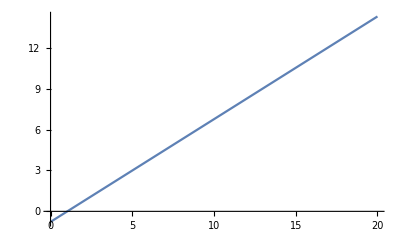

```mathematica
Plot[model["BestFit"],{x,0,20}]
```

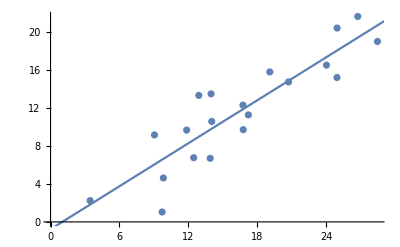

```mathematica
Show[ListPlot[data],Plot[model["BestFit"],{x,0,30}]]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.773591 | 1.60131 | -0.483099 | 0.634849
x | 0.753907 | 0.0899095 | 8.38518 | 1.24645×10^-7

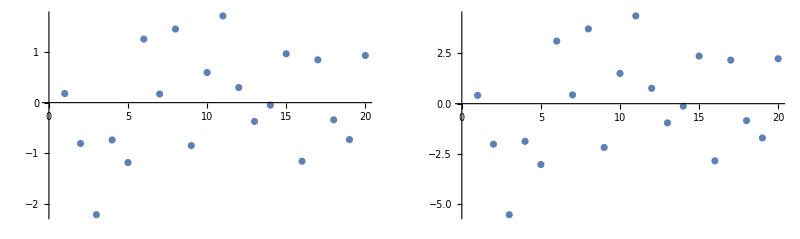

```mathematica
{sr,fr}=model[{"StandardizedResiduals","FitResiduals"}];
{{ListPlot[sr],ListPlot[fr]}}//GraphicsGrid
```

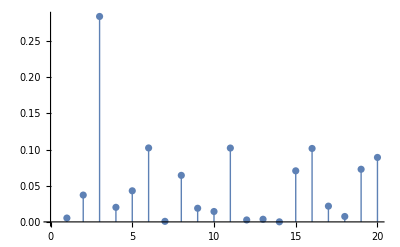

```mathematica
ListPlot[model["CookDistances"],Filling->Axis,FillingStyle->Thick,PlotStyle->Thick]
```

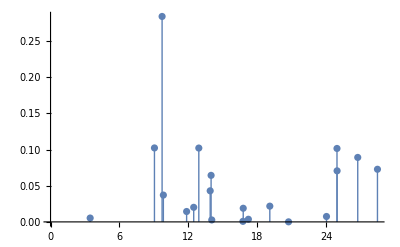

```mathematica
ListPlot[Transpose[{data[[All,1]],model["CookDistances"]}],Filling->Axis,FillingStyle->Thick,PlotStyle->Thick]
```

```mathematica
model["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}